```mathematica
(*1 er a CONIC er math *)
```

```mathematica
p:=5 x^2+2x*y+5 y^2+26x+34y+65
a=5;h=1;b=5;g=13;f=17;c=65;d=a*b*c+2f*g*h-a*f^2-b*g^2-c*h^2;
h1=a*b-h^2;
If[d==0,Print["Pairs of straight lines"],If[a==b&&h==0,Print["Circle"],If[d≠0&&a*b-h^2==0,Print["Parabola"],If[d≠0&&a*b-h^2>0,Print["Ellipse"],If[d≠0&&a*b-h^2<0,Print["Hyperbola"],If[d≠0&&a*b-h^2<0&&a+b==0,Print["Rectangular hyperbola"]]]]]]]
```

Ellipse

```mathematica
s=Solve[D[p,x]==0&&D[p,y]==0,{x,y}]
```

{{x→-2,y→-3}}

```mathematica
Print["The center of the ellipse is",{α=-2,β=-3}]
```

The center of the ellipse is{-2,-3}

```mathematica
c1=-d/h1;θ=1/2 ArcTan[(2h)/(a-b)];Print["The standard equation is",p==0/.{x->α+x Cos[θ]-y Sin[θ],y->β+x Sin[θ]+yCos[θ]}//Simplify]
```

Power::infy: Infinite expression 1/0 encountered.

The standard equation isIndeterminate==0

```mathematica
(*ImplicitPlot mathematica 5.2 er theke porer version e kaj kore na tai amra ekon theke ImplicitPlot er poriborte ContourPlot Babohar korbo link- https://reference.wolfram.com/language/Compatibility/tutorial/Graphics/ImplicitPlot.html *)
```

```mathematica
ContourPlot[{5 x^2+2x*y+5 y^2+26x+34y+65==0},{x,-4,6},{y,-8,8}];
```

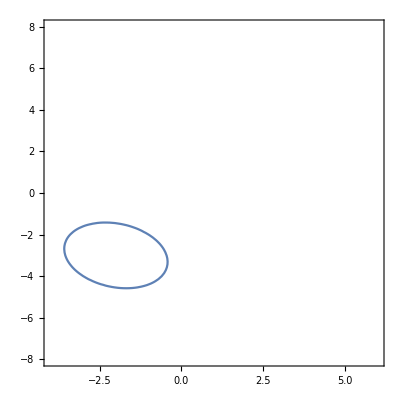

```mathematica
%26
```

```mathematica
ContourPlot[{y^2==x^3(2-x)},{x,-4,6},{y,-8,8}];
```

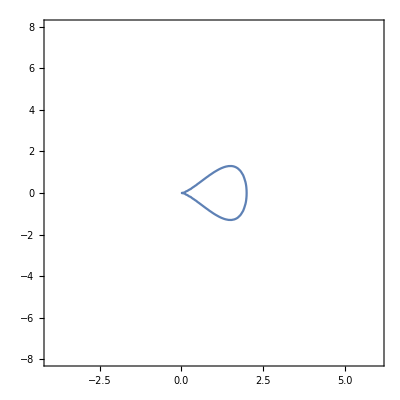

```mathematica
%28
```

```mathematica
ContourPlot[{x^2+y^2==5^2},{x,-8,8},{y,-8,8}];
```

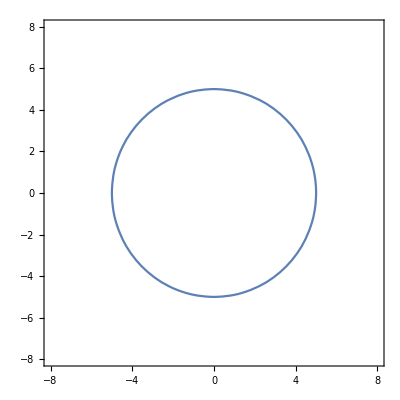

```mathematica
%32
```

```mathematica
(*The given is 
i) Show that 2x^2-3x*y-2 y^2-4x+8y represents a pair of straight lines .
ii) Find the point of intersection of the two lines.
 iii) Calculate the area of the triangular region bounded by the two lines and y-axis. 
*)
pol[x_,y_]=2x^2-3x*y-2 y^2-4x+8y;
a=2;b=-2;h=-3/2;g=-2;f=4;c=0;
del={{a,h,g},{h,b,f},{g,f,c}};
dt = Det[del];
If[dt==0,Print["pair of Straight Lines"],Print["not Pair of Straight Lines"]]
```

pair of Straight Lines

```mathematica
Factor[pol[x,y]]
```

(x-2 y) (-4+2 x+y)

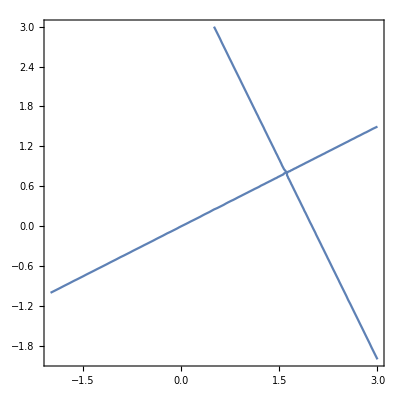

```mathematica
ContourPlot[pol[x,y]==0,{x,-2,3},{y,-2,3}]
```

```mathematica
Print["The point of intersection is ",pnt={(h*f-b*g)/(a*b-h^2),(h*g-a*f)/(a*b-h^2)}]
```

The point of intersection is {8/5,4/5}

```mathematica
a+b
```

0

```mathematica
(*Since a+b = 0 the angle between them is 90° *)
pol[x,y]/.x->0
```

8 y-2 y^2

```mathematica
Solve[%==0,y]
```

{{y→0},{y→4}}

```mathematica
(*The point of intersection on the y-axis are (0,0) & (0,4)*)
abc = {{0,0,1},{0,4,1},{8/5,4/5,1}};
area = 1/2*Abs[Det[abc]]//N
```

3.2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→InverseFunction[Rule,1,2][0,InverseFunction[Rule,1,2][0,InverseFunction[Rule,1,2][0,4]]]}}